g=2/3  Monte Carlo Simulation
Compare results of different initial states (MCMC)

```mathematica
fWu[y_, g_, energy_, mu_, kT_]:=
Module[{x,f},
x=Exp[(energy-mu)/kT];
f=y^g*(1+y)^(1-g)-x;
f
]

fWup[y_, g_]:=
Module[{fp},
fp=g*y^(g-1)*(1+y)^(1-g)+ (1-g)*y^g*(1+y)^(-g);
fp
]

PhiWu[y_, g_, energy_, mu_, kT_]:=
Module[{Phi},
Phi=y-fWu[y,g,energy,mu,kT]/fWup[y,g];
Phi
]

NiWu[g_, energy_, mu_, kT_]:=
Module[{ni,y,y1, Tol,Diff,n,n1},
y=1;
Tol=10^(-8);
Diff=1;
While[Diff>Tol,
y1=PhiWu[y, g, energy, mu, kT]//N;
n=1/(Re[y]+g);
n1=1/(Re[y1]+g);
Diff=Abs[n-n1];
(*Print[n1];*)
y=y1;
];
y=Re[y];
ni=1/(y+g);
ni
]

TotalParNum[g_,mu_,kT_, maxsum_]:=
Module[{N,ek},
N=0; (*N is the total particle number*) 
For[ek=1,ek≤maxsum,ek++, 
N=N+NiWu[g,ek,mu,kT];
(*Print[N];*)
];
N
]

ChemicalEnergy[g_,Nump_,Ef_,Tem_]:=Module[{tol,maxsum,mutry,k,mumin,mumax,nexit,nmax,Ntry,tol1,mu},
(*Print[Nump];*)
tol=10^(-7);
maxsum=0;
mutry=Ef+Tem;
For[k=Ef+1,k≤(Ef+1000),k++,
If[NiWu[g,k,mutry,Tem]≤tol,{maxsum=k;Break[]},0];
];
mumin=If[Tem≥0.5,Ef-3*Tem,Ef-1];
mumax=If[Tem≥0.5,Ef+Tem,Ef+1];
Ntry=TotalParNum[g,mutry,Tem, maxsum];
tol1=10^(-5);
nmax=1000;
nexit=1;
While[Abs[Ntry-Nump]>tol1,
If[nexit==nmax,{Print["error"];Break[]}];
If[Ntry-Nump<0,{mumin=mutry},{mumax=mutry}];
mutry=0.5*(mumin+mumax);
Ntry=TotalParNum[g,mutry,Tem, maxsum];
(*Print[mutry];*)
(*Print[Ntry];*)
(*Print[Abs[Ntry-Nump]];*)
nexit=nexit+1;
];
mu=mutry;
mu
]
```

Data importing finished

18

12

mu=

12.5

Ground state:

{2,1,2,1,2,1,2,1,2,1,2,1,0,0,0,0,0,0,0,0,0,0}

Excitation state 1:

{2,1,2,1,2,1,2,1,2,1,2,1,0,0,0,0,0,0,0,0,0,0}

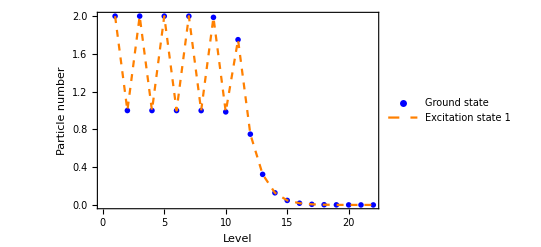

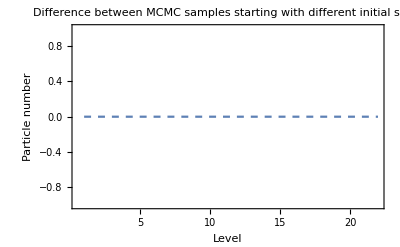

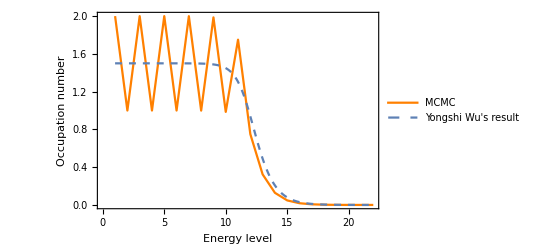

{{1,0.5},{2,0.5},{3,0.500001},{4,0.499993},{5,0.500016},{6,0.499883},{7,0.500139},{8,0.498222},{9,0.498534},{10,0.463808},{11,0.446986},{12,0.188414},{13,0.166121},{14,0.0782607},{15,0.0318847},{16,0.0117545},{17,0.00445186},{18,0.0017492},{19,0.000708686},{20,0.000215982},{21,0.000115455},{22,0.00004985}}

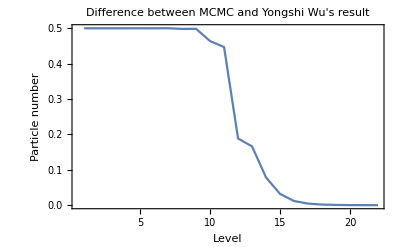

{1.5,1.5,1.5,1.49999,1.49997,1.49987,1.49941,1.49737,1.48832,1.44945,1.30354,0.938098,0.49004,0.206672,0.0798417,0.0298935,0.0110679,0.0040812,0.00150269,0.000552982,0.000203455,0.00007485}

```mathematica
StateMatrixE6=Import["2_3_data_T1.txt","Table"];
StateMatrix1E6=Import["2_3_data_T1.txt","Table"];
Print["Data importing finished"];
groundState23=StateMatrixE6[[1]];
kT=1; (*temperature*)
g=2/3;

Ntotal=Total[groundState23](*total number of particles*)
Ef=Length[Select[groundState23,#≠0&]] (*fermi energy; the eneryg of lowest level is 1*)

mu=ChemicalEnergy[g,Ntotal,Ef,kT];
Print["mu="];
Print[mu]




stateMatrixSize=10^6;
stateSize=Length[groundState23]; (* state length*)
NpMC=Table[0,{i,1,stateSize}];
For[i=1,i≤stateSize,i++,
NpMC[[i]]=Total[StateMatrixE6[[All,i]]]/stateMatrixSize
];
NpMC1=Table[0,{i,1,stateSize}];
For[i=1,i≤stateSize,i++,
NpMC1[[i]]=Total[StateMatrix1E6[[All,i]]]/stateMatrixSize
];
Diff=Abs[NpMC1-NpMC];

NpMCPlot=Table[0,{i,1,stateSize}];
NpMC1Plot=Table[0,{i,1,stateSize}];
DiffPlot=Table[0,{i,1,stateSize}];
For[i=1,i≤stateSize,i++,
NpMCPlot[[i]]={i,NpMC[[i]]};
NpMC1Plot[[i]]={i,NpMC1[[i]]};
DiffPlot[[i]]={i,Diff[[i]]};
];

Print["Ground state:"];
Print[StateMatrixE6[[1]]];
Print["Excitation state 1:"];
Print[StateMatrix1E6[[1]]];

plot1=ListPlot[NpMCPlot,Frame->True,FrameLabel->{"Level","Particle number"},PlotRange->{0,2},PlotStyle->{Blue},PlotMarkers->{"*",20},PlotLegends->{"Ground state"}];
plot2=ListLinePlot[NpMC1Plot,Frame->True,FrameLabel->{"Level","Particle number"},PlotRange->{0,2},PlotStyle->{Dashed,Orange},PlotLegends->{"Excitation state 1"}];
Print[Show[plot1,plot2]];
ListLinePlot[DiffPlot,Frame->True,FrameLabel->{"Level","Particle number"},PlotRange->All,PlotStyle->{Dashed},PlotLabel->"Difference between MCMC samples starting with different initial state"]


plot3=ListLinePlot[NpMC1Plot,Frame->True,FrameLabel->{Style["Energy level",20],Style["Occupation number",20]},PlotRange->{0,2},PlotStyle->{Orange},FrameTicksStyle->Directive[FontSize->15],PlotLegends->{"MCMC"}];

plot4=Plot[NiWu[g, x, mu, kT],{x,1,stateSize},Frame->True,FrameLabel->{Style["Energy level",20],Style["Occupation number",20]},PlotRange->{0,2},PlotStyle->{Dashed},PlotLegends->{"Yongshi Wu's result"}];
Print[Show[plot3,plot4]];

wudist = Table[0,{i,1,stateSize}];
Diff1=Table[0,{i,1,stateSize}];
Diff1Plot=Table[0,{i,1,stateSize}];
For[i=1,i≤stateSize,i++,
wudist[[i]]=NiWu[g, i, mu, kT];
Diff1[[i]]=Abs[NiWu[g, i, mu, kT]-NpMC[[i]]];
Diff1Plot[[i]]={i,Diff1[[i]]};
];
Print[Diff1Plot]
ListLinePlot[Diff1Plot,Frame->True,FrameLabel->{"Level","Particle number"},PlotRange->All,PlotLabel->"Difference between MCMC and Yongshi Wu's result"]
Print[wudist]
```

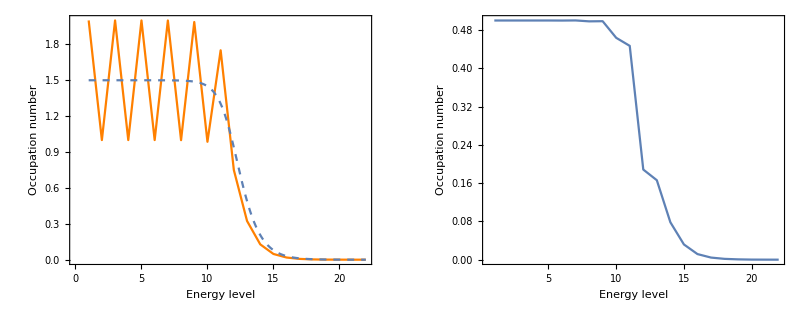

```mathematica
plot5=ListLinePlot[NpMC1Plot,Frame->True,FrameLabel->{Style["Energy level",20],Style["Occupation number",20]},PlotRange->{0,2},PlotStyle->{Orange},FrameTicksStyle->Directive[FontSize->15],PlotLegends->Placed[{Style["MCMC",17]},{0.25, 0.25}]];
plot6=Plot[NiWu[g, x, mu, kT],{x,1,stateSize},Frame->True,FrameLabel->{Style["Energy level", 20],Style["Occupation number", 20]},PlotRange->{0,2},PlotStyle->{Dashed},PlotLegends->Placed[{Style["Wu's distribution",17]},{0.25,0.25}]];
plot8=ListLinePlot[Diff1Plot,Frame->True,FrameLabel->{Style["Energy level", 20],Style["Occupation number", 20]},FrameTicksStyle->Directive[FontSize->15],PlotRange->All];
GraphicsRow[{Show[plot5,plot6],plot8}]
```

```mathematica
levels=Table[i,{i,1,stateSize}];
Print["levels"]
Print[levels]
energyGround=levels.StateMatrixE6[[1]];
Print["energy of the ground state"]
Print[energyGround]
energyg23=levels.NpMC-energyGround;
Print["MCMC:"]
Print[N[NpMC]]
Print["Wu's distribution:"]
Print[NiWu[g, levels, mu, kT]]
Print["energy of current temperature of g=2/3 with E_ground=0"]
Print[N[energyg23]]
```

levels

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22}

energy of the ground state

114

MCMC:

{2.,1.,2.,1.,1.99999,0.999986,1.99955,0.99915,1.98685,0.985644,1.75053,0.749684,0.323919,0.128411,0.047957,0.018139,0.006616,0.002332,0.000794,0.000337,0.000088,0.000025}

Wu's distribution:

{2.14281,2.14274,2.14253,2.14197,2.14044,2.1363,2.12513,2.09535,2.01846,1.83538,1.47235,0.957532,0.490924,0.211184,0.0828516,0.031243,0.0116006,0.00428227,0.00157735,0.000580545,0.000213607,0.0000785866}

energy of current temperature of g=2/3 with E_ground=0

1.17699